## Распределение вершин по слоям

Пусть G(V,A) – ациклический орграф, вершины которого необходимо распределить по слоям. Введём переменные x_ij

x_ij=Piecewise[{{1, вершина i∈j-ому слою}, {0, если нет}}]

Количество вершин на слое можно посчитать

w_j=∑_i x_ij

В таком случае за максимальную ширину слоя отвечает W

w_j≤W

Для каждой вершины i мы можем определить пару {(h̲)_i,(h̄)_i} минимально и максимального номера слоя, на котором может находить вершина. Создаются только переменные x_ij:(h̲)_i≤j≤(h̄)_i. Поскольку каждая вершин лежит только на одном слое, имеем

∑_(j=(h̲)_i)^((h̄)_i) x_ij=1

Чтобы узнать, на каком слое находится вершина, используем

h_i=∑_(j=(h̲)_i)^((h̄)_i) j×x_ij

В таком случае за количество слоёв отвечает H

h_i≤H

Не забываем про порядок ∀u->v∈A

h_v-h_u≥1

Ну, и, конечно, ограничение целочисленности

x_ij∈{0,1}

Соберём всё вместе.

В данной постановке мы можем 
1) минимизировать количество слоёв H при фиксированном W
2) минимизировать максимальную ширину слоя	W при фиксированном H
3) минимизировать взвешенную сумму H и W
	Пусть α∈[0,1] – параметр, отвечающий за значимость “высоты” и “ширины” графа, а H и W являются переменными или фиксированными по желанию пользователя. Тогда

α H+(1-α)W⟶min

∑_(k=(h̲)_v)^((h̄)_v) x_(v,k)=1,        ∀v∈V

∑_(k=(h̲)_v)^((h̄)_v) k x_(v,k)≤H,        ∀v∈V

∑_(v∈V) x_(v,k)≤W,        ∀1≤k≤h_max

∑_(k=(h̲)_v)^((h̄)_v) k x_(v,k)-∑_(k=(h̲)_v)^((h̄)_v) k x_(u,k)≥1,        ∀u->v∈A

x_(v,k)∈{0,1},         ∀v∈V∀1≤k≤h_max

где h_max – параметр, определяемый пользователем – максимально допустимое число слоёв (для которых вообще будут создаваться переменные).

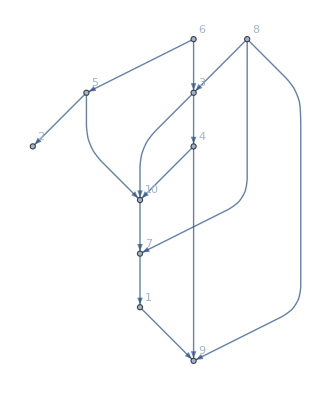

```mathematica
SeedRandom[52]
graph=RandomGraph[{10,14},DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
Clear[LongestPathLength]
LongestPathLength::"usage"="Ищет длину длиннейшего пути в графе";
LongestPathLength[graph_/;VertexCount[graph]==1]:=0
LongestPathLength[graph_]:=With[{inc=Transpose@IncidenceMatrix@graph},
Max@LinearProgramming[Total@inc,inc,ConstantArray[1,EdgeCount@graph]]]
```

```mathematica
Clear[strangeGetLayers]

Options[strangeGetLayers]={
MaxLayer->Automatic,
MaxWidth->Automatic,
MaxHeight->Automatic,
Intervals->Automatic,
Alpha->1/2
};

strangeGetLayers[graph_,OptionsPattern[]]:=Module[
{flat,vars,vertices,res,gr,
hMax,hLow,hHigh,
x,H,W,α=OptionValue[Alpha],
r2,r3,r4,r5,r6,tmp
},

vertices=VertexList@graph;

hMax=If[
OptionValue[MaxLayer]===Automatic,
LongestPathLength@graph,
OptionValue[MaxLayer]
];

If[
OptionValue[Intervals]===Automatic,

hLow=Table[LongestPathLength@Subgraph[graph,VertexInComponent[graph,{vertex}]],{vertex,vertices}]+1;
hHigh=hMax-Table[LongestPathLength@Subgraph[graph,VertexOutComponent[graph,{vertex}]],{vertex,vertices}]+1,

{hLow,hHigh}=Transpose@OptionValue[Intervals]
];

If[OptionValue[MaxWidth]=!=Automatic,W=OptionValue[MaxWidth]];
If[OptionValue[MaxHeight]=!=Automatic,H=OptionValue[MaxHeight]];

vars=MapThread[Thread[x[#,Range[#2,#3]]]&,{vertices,hLow,hHigh}];
flat=Flatten@vars;

tmp=MapThread[Dot,{vars,vars⟦All,All,2⟧}];(*сумма из (3)*)
r2=Thread[Total[vars,{2}]==1];
r3=Thread[tmp≤H];
r4=Values@GroupBy[flat,Last,Total[#]≤W&];
r5=Table[tmp⟦arc⟦2⟧⟧-tmp⟦arc⟦1⟧⟧≥1,{arc,EdgeList@graph}];
r6=Join[Thread[0≤flat],Thread[flat≤1],Table[Element[v,Integers],{v,flat}]];

res=If[
OptionValue[MaxWidth]===Automatic,
If[
OptionValue[MaxHeight]===Automatic,
Quiet@LinearOptimization[α H+(1-α)W,Join[r2,r3,r4,r5,r6],Join[flat,{H,W}]],
Quiet@LinearOptimization[W,Join[r2,r3,r4,r5,r6],Append[flat,W]]
],
Quiet@LinearOptimization[H,Join[r2,r3,r4,r5,r6],Append[flat,H]]
];
gr=GroupBy[Pick[Keys@res,Values@res,1],Last->First];
gr/@Sort@Keys@gr
]
```

```mathematica
strangeGetLayers[graph]
```

{{6,8},{3,5},{2,4},{10},{7},{1},{9}}